## Condensate (Zero- order solutions)

```mathematica
DSolve[{U''[t]+2 g^2 U[t]^3==0},U,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{U→Function[{t},-(ⅈ √(-g/(√C[1])) √C[1] JacobiSN[√(g t^2 √C[1]+2 g t √C[1] C[2]+g √C[1] C[2]^2),-1])/g]},{U→Function[{t},(ⅈ √(-g/(√C[1])) √C[1] JacobiSN[√(g t^2 √C[1]+2 g t √C[1] C[2]+g √C[1] C[2]^2),-1])/g]}}

```mathematica
(*Taking √Subscript[c, 1]=g Subscript[c, 3]^2, we get U(t)=Subscript[c, 3] JacobiSN[Subscript[gc, 3](t+Subscript[c, 2]),-1]*)
```

```mathematica
U[t_]=c1 JacobiSN[g c1(t+c2),-1]
```

c1 JacobiSN[c1 g (c2+t),-1]

```mathematica
U''[t]+2 g^2 U[t]^3//FullSimplify
```

0

```mathematica
U[0]
```

(c1^(1/4) JacobiSN[c2 √(√c1 g),ⅈ])/(√g)

```mathematica
U'[0]
```

(c1^(1/4) √(√c1 g) JacobiCN[c2 √(√c1 g),ⅈ] JacobiDN[c2 √(√c1 g),ⅈ])/(√g)

```mathematica
Solve[(c1^(1/4) JacobiSN[c2 √(√c1 g),ⅈ])/(√g)==0&&(c1^(1/4) √(√c1 g) JacobiCN[c2 √(√c1 g),ⅈ] JacobiDN[c2 √(√c1 g),ⅈ])/(√g)==0, {c1,c2}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -(InverseJacobiCN[JacobiCN[c1^(1/4) c2 √g,ⅈ],ⅈ]^4)/g^(3/2) == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is (InverseJacobiCN[JacobiCN[c1^(1/4) c2 √g,ⅈ],ⅈ]^4)/(√g) == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is (InverseJacobiCN[JacobiCN[c1^(1/4) c2 √g,ⅈ],ⅈ]^4)/g == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c1→0}}

```mathematica
(*Maple solution*)
```

```mathematica
U(t)=c2 JacobiSN[c2(gt+c1),-1]
```

```mathematica
(* for U'[0] not zero*)
```

```mathematica
u[t_]=JacobiSN[g t,-1];
```

```mathematica
(*For Subscript[ψ, 1L1] and Subscript[ψ, 2L2]*)
```

```mathematica
DSolve[ D[p[t],t]+I/2 g u[t]p[t]==0,p,t]
```

{{p→Function[{t},ⅇ^(1/2 ⅈ ArcTan[JacobiCD[g t,-1]]) C[1]]}}

```mathematica
(*Maple solution*)
```

```mathematica
p(t)=c1 1/(√(JacobiDN[t,-1]-I JacobiCN[t,-1]))
```

```mathematica
(*Initial conditions for both functions*)
```

```mathematica
N[1/(√(JacobiDN[0,-1]-I JacobiCN[0,-1]))]
```

0.776887+0.321797 ⅈ

```mathematica
N[ⅇ^(1/2 ⅈ ArcTan[JacobiCD[ 0,-1]])]
```

0.92388+0.382683 ⅈ

```mathematica
(*Plots for both solutions(For comparision)*)
```

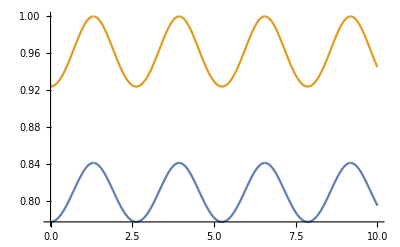

```mathematica
Plot[{Re[1/(√(JacobiDN[t,-1]-I JacobiCN[t,-1]))],Re[ⅇ^(1/2 ⅈ ArcTan[JacobiCD[ t,-1]])]},{t,0,10}]
```

```mathematica
(* For Subscript[ψ, 1L2],Subscript[ψ, 2L1]*)
```

```mathematica
eqns={I D[q[t],t]- g u[t]r[t]+1/2 g u[t]q[t]==0,I D[r[t],t]- g u[t]q[t]+1/2 g u[t]r[t]==0};
```

```mathematica
DSolve[eqns,{q,r},t]
```

DSolve[{1/2 g JacobiSN[g t,-1] q[t]-g JacobiSN[g t,-1] r[t]+ⅈ q'[t]==0,-g JacobiSN[g t,-1] q[t]+1/2 g JacobiSN[g t,-1] r[t]+ⅈ r'[t]==0},{q,r},t]

```mathematica
(*Maple solutions*)
```

```mathematica
q1[t_]=c1(JacobiDN[g t,-1]-I JacobiCN[g t,-1])^(3/2)+c2(JacobiDN[g t,-1]-I JacobiCN[g t,-1])^(-1/2);
```

```mathematica
r1[t_]=-c1(JacobiDN[g t,-1]-I JacobiCN[g t,-1])^(3/2)+c2(JacobiDN[g t,-1]-I JacobiCN[g t,-1])^(-1/2);
```

```mathematica
I D[q1[t],t]- g u[t]r1[t]+1/2 g u[t]q1[t]//FullSimplify
```

0

```mathematica
I D[r1[t],t]- g u[t]q1[t]+1/2 g u[t]r1[t]//FullSimplify
```

0

```mathematica
(*PLots-bilinears*)
```

```mathematica
c1=1;c2=0;g=0.333;
```

```mathematica
r1[t]
```

-(-ⅈ JacobiCN[0.333 t,-1]+JacobiDN[0.333 t,-1])^(3/2)

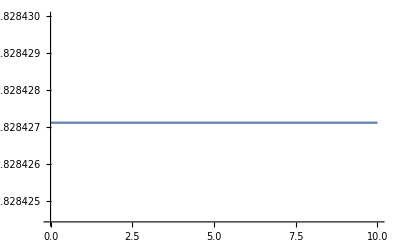

```mathematica
Plot[r1[t]Conjugate[r1[t]],{t,0,10},PlotRange->{Full,{2.82842444,2.82843}}]
```